```mathematica
NN = 100
```

100

```mathematica
f3[α_] := 1/NN∑_(k=0)^(NN-1) 1/(1 - α ⅇ^(2 π ⅈ k/NN))
```

```mathematica
f4[α_] := 1/(1 - α^NN)
```

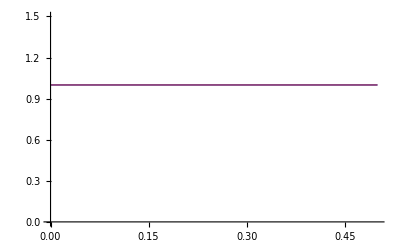

```mathematica
Plot[{f3[α], f4[α]}, {α, 0.0, 0.5}, PlotRange->{0.0, 1.5}]
```

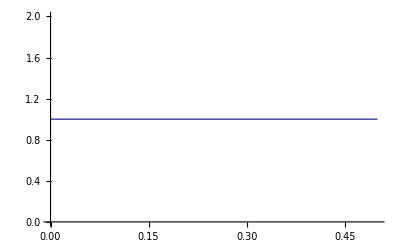

```mathematica
Plot[f4[α], {α, 0.0, 0.5}]
```

```mathematica
f3[0.4]
```

1.-2.52576×10^-17 ⅈ

```mathematica
f4[0.4]
```

1.

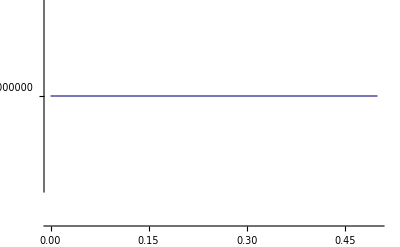

```mathematica
Plot[f3[α],{α, 0.0, 0.5}]
```

```mathematica
f1[α_] := 1/NN∑_(k=0)^(NN-1) 1/((1 + α^2) - 2α Cos[2(π k)/NN])
```

```mathematica
f2[α_] := 1/NN 1/(1 - α^2)( (2 NN)/(1 - α^NN) - NN )
```

```mathematica
f22[α_] := 1/(1 - α^2)
```

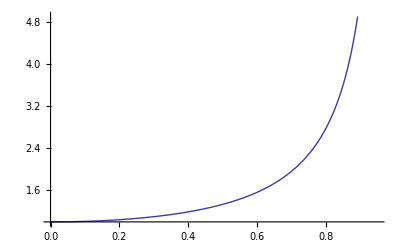

```mathematica
Plot[f1[α], {α, 0, 0.95}]
```

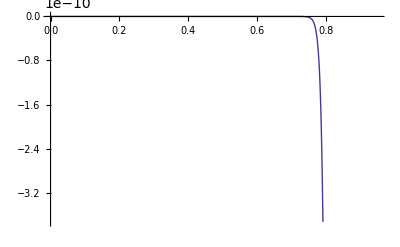

```mathematica
Plot[f22[α] - f1[α], {α, 0.0, 0.95}]
```

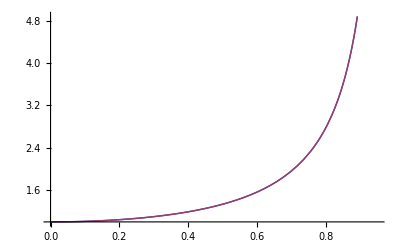

```mathematica
Plot[{f1[α],f2[α]},{α, 0, 0.95}]
```

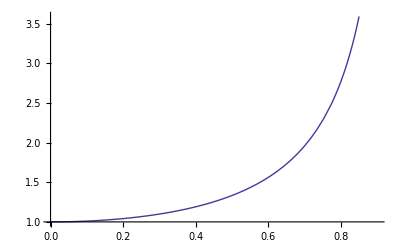

```mathematica
Plot[f2[α],{α,0,0.9}]
```

```mathematica
f1[0.2] // N
```

0.964396